```mathematica
(*From sequence of steps 1+1+2+2+3+3+......*)
(*Algorithm: 1. Find smallest n such that N-n(n+1)<0
2. Calculate mod(n,2), if equals 0 then the direction is (left, down), if equals 1 then it is (right, up)
3. If N-n^2≤ 0-> Horizontal, If N-n^2>0-> Vertical*)
step[initial_,N_]:=Module[{n,direction},
If[N==0,Return[initial],
n=Ceiling[n]/.NSolve[N-n(n+1)==0 && n>0][[1]];
Which[Mod[n,2]==0 && N-n^2≤ 0,direction={-1,0},Mod[n,2]==1 && N-n^2≤ 0, direction={1,0}, Mod[n,2]==0 && N-n^2> 0,direction={0,-1},
Mod[n,2]==1&& N-n^2>0, direction={0,1}];
initial+direction]];
DiscreteSpiral[N_]:=Module[{points={{0,0}}},
Do[AppendTo[points,step[points[[-1]],i]],{i,N}];
points];
```

{{0,0},{1,0},{1,1},{0,1},{-1,1},{-1,0}}

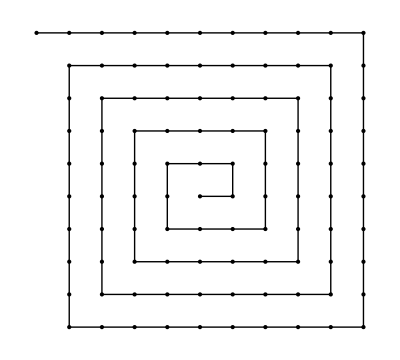

```mathematica
With[{pts=DiscreteSpiral[100]},Graphics[{Point[pts],Line[pts]}]]
```